```mathematica
(*parameters*)
q=0.067;κ=3.41;
γ1=13.38;γ2=4.24;γ3=5.69;
av=2.0;
bv=-2.16;
dv=-6.06;
γh=3.56;
ηh=0.20;
λ=κ γ2-2ηh γ3^2;
λp=κ γ2-2ηh γ3 γ2;
ϵzz=0.45/100;ϵxx=-0.61/100;ϵyy=-0.61/100;
ΔLH=2 bv (ϵxx/2+ϵyy/2-ϵzz);
ℏ=6.582*10^(-16);
LxH=45*10^(-9);
LyH=45*10^(-9);
px2=ℏ^2/(2 LxH^2);py2=ℏ^2/(2 LyH^2);
m0=9.11*10^(-31);
ec=1.6*10^(-19);
ℏJ=6.626/(2Pi)*10^(-34);
```

```mathematica
(*ψxH[x_,n_]:=1/Sqrt[2^n n!]1/Sqrt[LxH Sqrt[Pi]]Exp[-x^2/(2 LxH^2)]HermiteH[n,x/LxH]
ψyH[x_,n_]:=1/Sqrt[2^n n!]1/Sqrt[LyH Sqrt[Pi]]Exp[-x^2/(2 LyH^2)]HermiteH[n,x/LyH]*)
```

```mathematica
(*Assuming[LxH>0,Refine[Integrate[ψxH[x,0]x^2 ψxH[x,0],{x,-∞,∞}]//FullSimplify]]
Assuming[LxH>0,Refine[-Integrate[ψxH[x,0]D[ψxH[x,0],{x,2}],{x,-∞,∞}]//FullSimplify]]*)
```

```mathematica
gt={{3q,0,0},{0,-3q,0},{0,0,6κ+27/2q-2γh}};
```

```mathematica
NSolve[3q+6bv κ/ΔLH(ϵyy-ϵxx*(1+x))==0,x]
```

{{x→0.0294102}}

{{x→0.038875}}

{{x→0.0341426}}

```mathematica
(ϵyy-ϵxx*(1+x))/((ϵyy+ϵxx*(1+x)))/.{{x->0.029410188612726956},{x->0.03887498998445588},{x->0.0341426}}
```

{-0.014492,-0.0190669,-0.0167848}

```mathematica
δgt={{6bv κ/ΔLH(ϵyy-ϵxx*1.0341426),0,0},{0,6bv κ/ΔLH(ϵyy-ϵxx*1.0341426),0},{0,0,0}};
```

```mathematica
δgxx=6 ec/(m0*ΔLH)*(λ px2-λp py2);
δgyy=-6 ec/(m0*ΔLH)*(λ py2-λp px2);
```

```mathematica
smallg={0.011,0.028,0.003,0.0056,0.070,0.042,0.009,0.029,0.051,0.030};
largeg={0.423,0.362,0.37,0.453,0.450,0.414,0.419,0.395};
```

```mathematica
δgt2=DiagonalMatrix[{δgxx,δgyy,0}];
```

```mathematica
gt2fs[σe_]:=Module[{dllist=RandomVariate[NormalDistribution[0,σe*10^(-5)],{200,3,3}]},Table[gt+δgt+{
{6bv κ/ΔLH(dl[[2,2]]-dl[[1,1]]),4 Sqrt[3]dv κ/ΔLH(dl[[1,2]]+dl[[2,1]])/2,0 },{-4 Sqrt[3]dv κ/ΔLH(dl[[1,2]]+dl[[2,1]])/2,6bv κ/ΔLH(dl[[2,2]]-dl[[1,1]]),0},{-4 Sqrt[3]dv κ/ΔLH(dl[[1,3]]+dl[[3,1]])/2 ,-4 Sqrt[3]dv κ/ΔLH(dl[[2,3]]+dl[[3,2]])/2,0}
},{dl,dllist}]]
```

```mathematica
gt2f[σl_]:=Module[{dllist=Abs[RandomVariate[NormalDistribution[LxH,σl*10^(-9)],{1000,2}]]},Table[gt+δgt+DiagonalMatrix[{6 ec/(m0*ΔLH)*(λ ℏ^2/(2 (dl[[1]])^2)-λp ℏ^2/(2 (dl[[2]])^2)),-6 ec/(m0*ΔLH)*(λ ℏ^2/(2 (dl[[2]])^2)-λp ℏ^2/(2 (dl[[1]])^2)),0}],{dl,dllist}]]
```

```mathematica
angle[arg1__,arg2__]:=ArcCos[arg1.arg2/Norm[arg1]/Norm[arg2]]
```

```mathematica
dataG=Table[{ϕ,Mean[Map[Norm[{Cos[ϕ],Sin[ϕ],0}.#]&,gt2f[7]]],StandardDeviation[Map[Norm[{Cos[ϕ],Sin[ϕ],0}.#]&,gt2f[7]]]},{ϕ,0,Pi,0.01}];
```

```mathematica
data2DGs=Table[{ϕ,Mean[Map[Norm[{Sin[ϕ],Cos[ϕ],0}.#]&,gt2fs[1.]]],StandardDeviation[Map[Norm[{Sin[ϕ],Cos[ϕ],0}.#]&,gt2fs[1.]]]},{ϕ,Array[#&,400,{0.,Pi}]}];
```

```mathematica
data2DPhis=Table[{ϕ,Mean[Map[(angle[{Sin[ϕ],Cos[ϕ],0}.(gt+δgt),{Sin[ϕ],Cos[ϕ],0}.#]/Degree)&,gt2fs[1.]]],StandardDeviation[Map[(angle[{Sin[ϕ],Cos[ϕ],0}.(gt+δgt),{Sin[ϕ],Cos[ϕ],0}.#]/Degree)&,gt2fs[1.]]]},{ϕ,Array[#&,400,{0.,Pi}]}];
```

```mathematica
LaunchKernels[4]
```

{Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
(*data3DGs=ParallelTable[{ϕ,θ,Mean[Map[Norm[{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.#]&,gt2fsWithZ[1.]]],StandardDeviation[Map[Norm[{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.#]&,gt2fsWithZ[1.]]]},{ϕ,Array[#&,201,{0.,2Pi}]},{θ,Array[#&,101,{0.,Pi}]}];*)
```

```mathematica
data3DGsZoom=ParallelTable[{ϕ,θ,Mean[Map[Norm[{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.#]&,gt2fs[1.]]],StandardDeviation[Map[Norm[{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.#]&,gt2fs[1.]]]},{ϕ,Array[#&,201,{0.,2Pi}]},{θ,Array[#&,101,{Pi/2-2. Degree,Pi/2+2. Degree}]}];
```

```mathematica
(*data3DPhis=ParallelTable[{ϕ,θ,Mean[Map[(angle[{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.(gt+δgt),{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.#]/Degree)&,gt2fsWithZ[1.]]],StandardDeviation[Map[(angle[{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.(gt+δgt),{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.#]/Degree)&,gt2fsWithZ[1.]]]},{ϕ,Array[#&,201,{0.,2Pi}]},{θ,Array[#&,101,{0.,Pi}]}];*)
```

```mathematica
data3DPhisZoom=ParallelTable[{ϕ,θ,Mean[Map[(angle[{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.(gt+δgt),{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.#]/Degree)&,gt2fs[1.]]],StandardDeviation[Map[(angle[{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.(gt+δgt),{Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}.#]/Degree)&,gt2fs[1.]]]},{ϕ,Array[#&,201,{0.,2Pi}]},{θ,Array[#&,101,{Pi/2-2. Degree,Pi/2+2. Degree}]}];
```

```mathematica
CloseKernels[];
```

```mathematica
(*ListDensityPlot[{Flatten[data3DGs,1][[All,1]],Flatten[data3DGs,1][[All,2]],Flatten[data3DGs,1][[All,3]]}ᵀ,PlotRange->All,PlotLegends->Automatic]
ListDensityPlot[{Flatten[data3DGs,1][[All,1]],Flatten[data3DGs,1][[All,2]],Flatten[data3DGs,1][[All,4]]}ᵀ,PlotRange->All,PlotLegends->Automatic]*)
```

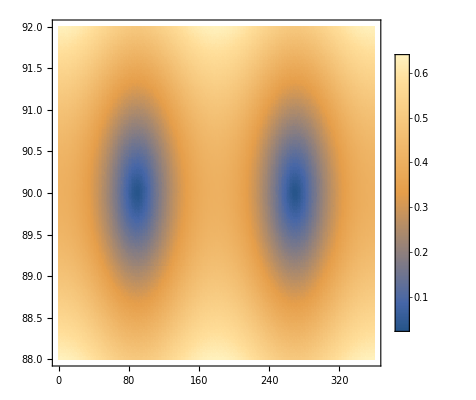

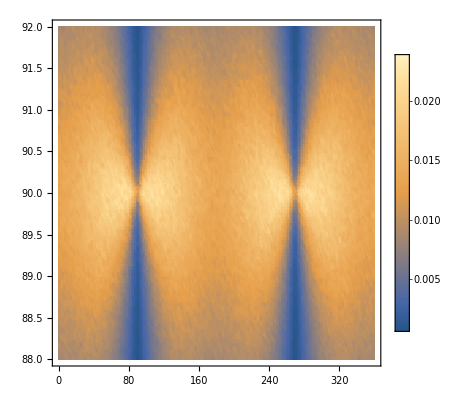

```mathematica
ListDensityPlot[{Flatten[data3DGsZoom,1][[All,1]]/ Degree,Flatten[data3DGsZoom,1][[All,2]]/ Degree,Flatten[data3DGsZoom,1][[All,3]]}ᵀ,PlotRange->All,PlotLegends->Automatic]
ListDensityPlot[{Flatten[data3DGsZoom,1][[All,1]]/ Degree,Flatten[data3DGsZoom,1][[All,2]]/ Degree,Flatten[data3DGsZoom,1][[All,4]]}ᵀ,PlotRange->All,PlotLegends->Automatic]
```

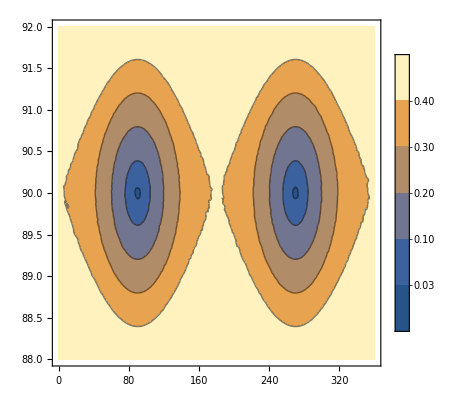

```mathematica
ListContourPlot[{Flatten[data3DGsZoom,1][[All,1]]/ Degree,Flatten[data3DGsZoom,1][[All,2]]/ Degree,Flatten[data3DGsZoom,1][[All,3]]}ᵀ,PlotRange->All,PlotLegends->Automatic,Contours->{0.03,0.1,0.2,0.3,0.4}]
```

```mathematica
Export["C:\\Users\\mruss\\Documents\\ProjectV1_gfactor_modeling\\variability\\variability_gfactor.csv",{Flatten[data3DGsZoom,1][[All,1]],Flatten[data3DGsZoom,1][[All,2]],Flatten[data3DGsZoom,1][[All,3]],Flatten[data3DGsZoom,1][[All,4]]}ᵀ,"CSV"]
```

C:\Users\mruss\Documents\ProjectV1_gfactor_modeling\variability\variability_gfactor.csv

```mathematica
(*ListDensityPlot[{Flatten[data3DPhis,1][[All,1]],Flatten[data3DPhis,1][[All,2]],Flatten[data3DPhis,1][[All,3]]}ᵀ,PlotRange->All,PlotLegends->Automatic]
ListDensityPlot[{Flatten[data3DPhis,1][[All,1]],Flatten[data3DPhis,1][[All,2]],Flatten[data3DPhis,1][[All,4]]}ᵀ,PlotRange->All,PlotLegends->Automatic]*)
```

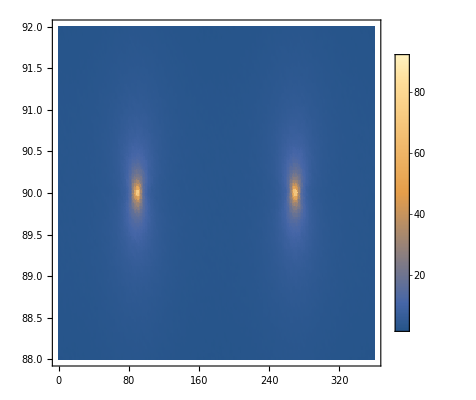

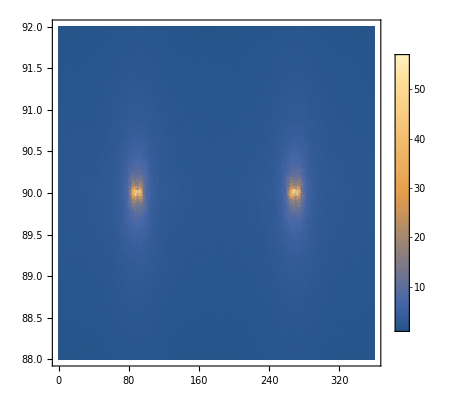

```mathematica
ListDensityPlot[{Flatten[data3DPhisZoom,1][[All,1]]/ Degree,Flatten[data3DPhisZoom,1][[All,2]]/ Degree,Flatten[data3DPhisZoom,1][[All,3]]}ᵀ,PlotRange->All,PlotLegends->Automatic]
ListDensityPlot[{Flatten[data3DPhisZoom,1][[All,1]]/ Degree,Flatten[data3DPhisZoom,1][[All,2]]/ Degree,Flatten[data3DPhisZoom,1][[All,4]]}ᵀ,PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Export["C:\\Users\\mruss\\Documents\\ProjectV1_gfactor_modeling\\variability\\variability_quant.csv",{Flatten[data3DPhisZoom,1][[All,1]]/ Degree,Flatten[data3DPhisZoom,1][[All,2]]/ Degree,Flatten[data3DPhisZoom,1][[All,3]],Flatten[data3DPhisZoom,1][[All,4]]}ᵀ,"CSV"]
```

C:\Users\mruss\Documents\ProjectV1_gfactor_modeling\variability\variability_quant.csv